#### Import MGenPackage

```mathematica
Block[{$Path=Append[$Path,NotebookDirectory[]]},
<<MGenPackage`]
```

#### Read all flute MIDI files in the Flute MIDI directory and convert them to a note coded string

```mathematica
text=StringJoin[fromMIDIFileToCodedNoteString/@FileNames["*.mid",FileNameJoin[{NotebookDirectory[],"Flute MIDI"}]]];
text//Short[#,5]&
```

```mathematica
text=StringJoin[fromMIDIFileToCodedNoteString/@{"/Users/peter.sjogren/Google Drive/Mathematica/bach/Flute MIDI/flute.mid","/Users/peter.sjogren/Google Drive/Mathematica/bach/Flute MIDI/fp-1all.mid","/Users/peter.sjogren/Google Drive/Mathematica/bach/Flute MIDI/fp-2cou.mid",(*"/Users/peter.sjogren/Google Drive/Mathematica/bach/Flute MIDI/fp-3sar.m_notuse_id.mid",*)"/Users/peter.sjogren/Google Drive/Mathematica/bach/Flute MIDI/fp-4bou.mid"}];
text//Short[#,5]&
```

S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S+++d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    h+++f+]+h+f+h+d+c+d+f+d+c+a+S+a+c+d+f+]+h+f+h+d+_+++]h]hf++…X+++Q+\+Q+`+d+++d+c+d+++]+++b+++a+++g+++f+++`+++S+++e+++d+++e+d+b+`+S+Q+\+Q+S+\+X+Z+\+Q+S+\+S+b+b+S+b+e+e+b+e+h+h+_+d+++l+++_+]+l+_+]+h+]+++++++++++

```mathematica
characters=Union[Characters[text]]
```

Characters[            S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S+++d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    h+++f+]+h+f+h+d+c+d+f+d+c+a+S+a+c+d+f+]+h+f+h+d+_+++]h]hf+++    f++ h+d+f+h+]+h+f+d+a+d+c+f+d+h+f+d+f+d+f+h+]+h+f+d+S+c+a+d+c+f+d+c+fdc+d+++++h+f+d+^+h+f+d+m+  d+  c+d+f+S+c+a+S+R+S+_+^+h+f++ d++ c f+d+c+a d+c+a+S+R+S++ aSR+S++++ c+a+S+a+c+d+f+h+f+h++ ]hf+h+++++_+^+h+^+_+m+o+p+o+p++ om_+m+++_^h+^+++g++++++++ f+d+c+a+S+R+S e+++f+++++d+c+a+c S+a+c+d+h+f+d+f _+^+h+f+d+c+a+S++++++++   S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S+++d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    h+++f+]+h+f+h+d+c+d+f+d+c+a+S+a+c+d+f+]+h+f+h+d+_+++]h]hf+++    f++ h+d+f+h+]+h+f+d+a+d+c+f+d+h+f+d+f+d+f+h+]+h+f+d+S+c+a+d+c+f+d+c+fdc+d+++++h+f+d+^+h+f+d+m+  d+  c+d+f+S+c+a+S+R+S+_+^+h+f++ d++ c f+d+c+a d+c+a+S+R+S++ aSR+S++++ c+a+S+a+c+d+f+h+f+h++ ]hf+h+++++_+^+h+^+_+m+o+p+o+p++ om_+m+++_^h+^+++g++++++++ f+d+c+a+S+R+S e+++f+++++d+c+a+c S+a+c+d+h+f+d+f _+^+h+f+d+c+a+S++++++++   S++ f+++    f+++    f ]+h+f+d+c+a+S+_ d+c+d+f+]+h+f+h++ d++     c++ h+++    h+++    h _+]+h+f+e+c+a+m f+e+f+h+_+]+h+]+  f+      a++ b a+b+d+b+a+S+Q+\+S+Q+a+S+b+a+S+a S+a+b+a+S+Q+\+Z+Q+\+S+Q+a+S+Q+S+Q+S++++ b+a+S+e+b+a+S h++ S++ Q+S+a Z Q+  \+  Z++++++     a++ c f+d+c+d a+S+a+b S+b+f+_ b+a+S+a d+b+a+b S+Q+S+a Q+a+d+] h+f+d+c f+h+]+a f+h+]+S+a+c+d+f+h+]+h h d ] d _+  ] h ]h]hf++     S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S++ d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    S++ a Q+\+Q+S+a+c+d+f+h+]+_+] h f d c S+R+S+a+c+d+f+h+]+_+m+_ ] h f d a+S+a+c+d+f+h+]+_+m+n+m _ ] h f _+]+h+]+h+f+d+c h+f+d+f+d+c+a+S+++a+c+d+f+h+]+_++++++++ h+f+d+c+a+S+a+c+d+f+h+]++++++++ c+d+f+h d+f+h+f ]+h+f+d+c+a+S+a+c+d+f+h+]+_+d+h+f+d+c+c+++d+++++++S++ f+++    f+++    f ]+h+f+d+c+a+S+_ d+c+d+f+]+h+f+h++ d++     c++ h+++    h+++    h _+]+h+f+e+c+a+m f+e+f+h+_+]+h+]+  f+      a++ b a+b+d+b+a+S+Q+\+S+Q+a+S+b+a+S+a S+a+b+a+S+Q+\+Z+Q+\+S+Q+a+S+Q+S+Q+S++++ b+a+S+e+b+a+S+h++ S++ Q+S+a Z Q+  \+  Z++++++     a++ c f+d+c+d a+S+a+b S+b+f+_ b+a+S+a d+b+a+b S+Q+S+a Q+a+d+] h+f+d+c f+h+]+a f+h+]+S+a+c+d+f+h+]+h h d ] d _+  ] h ]h]hf++     S++ d++     d++     d+h+f+d+c+a+S+Q S+d+c+a+S+  Q+  SQSQ\+++    S++ d+c+d+++fdc+d++++ h+f+d+c+a+S+Q+S+d+c+a+S+  Q+  SQSQ\+++    S++ a Q+\+Q+S+a+c+d+f+h+]+_+] h f d c S+R+S+a+c+d+f+h+]+_+m+_ ] h f d a+S+a+c+d+f+h+]+_+m+n+m _ ] h f _+]+h+]+h+f+d+c h+f+d+f+d+c+a+S+++a+c+d+f+h+]+_++++++++ h+f+d+c+a+S+a+c+d+f+h+]++++++++ c+d+f+h d+f+h+f ]+h+f+d+c+a+S+a+c+d+f+h+]+_+d+h+f+d+c+c+++d+++++++                                                          d+]+h+]+l+]+d+Q+d+]+h+]+l+]+d+Q+`+d+e+\+e+d+b+`+d+h+]+X+b+`+S+Q+`+d+e+\+e+d+b+`+d+h+]+X+b+`+S+Q+`+\+Q+Y+b+\+Q+X+`+\+Q+V+`+S+Q+\+X+\+S+d+h+_+n+q+n+_+h+d+b+`+S+`+Q+`+d+]+l+p+e+g+^+g+d+`+R+Q+[+Q+Y+Q+`+b+e+]+`+S+[+S+b+d+g+_+b+`+Q+`+d+e+]+l+d+b+S+b+f+g+_+n+e+d+g+l+_+l+p+l+g+`+g+l+_+l+p+l+g+`+g+^+]+^+p+^+g+`+g+^+]+^+p+^+g+a+g+^+]+^+p+^+g+a+g+d+a+Q+[+Y+X+V+g+e+d+e+]+e+b+S+\+S+b+d+b+`+S+`+d+]+h+]+l+]+f+c+S+c+f+_+]+g+f+g+f+d+g+Q+d+g+l+f+d+b+f+[+b+f+_+d+b+`+d+Z+d+f+]+c+S+`+Q+W+`+S+Q+[+d+e+b+\+e+d+b+Q+f+g+d+R+g+f+d+c+_+h+b+a+]+f+`+S+g+d+R+Q+f+c+Q+[+d+`+Q+Z+`+Q+Z+W+Z+Q+`+S+]+g+f+g+fd_+l+f+++++d+d+++++++++++++++  d+]+h+]+l+]+d+Q+d+]+h+]+l+]+d+Q+`+d+e+\+e+d+b+`+d+h+]+X+b+`+S+Q+`+d+e+\+e+d+b+`+d+h+]+X+b+`+S+Q+`+\+Q+Y+b+\+Q+X+`+\+Q+V+`+S+Q+\+X+\+S+d+h+_+n+q+n+_+h+d+b+`+S+`+Q+`+d+]+l+p+e+g+^+g+d+`+R+Q+[+Q+Y+Q+`+b+e+]+`+S+[+S+b+d+g+_+b+`+Q+`+d+e+]+l+d+b+S+b+f+g+_+n+e+d+g+l+_+l+p+l+g+`+g+l+_+l+p+l+g+`+g+^+]+^+p+^+g+`+g+^+]+^+p+^+g+a+g+^+]+^+p+^+g+a+g+d+a+Q+[+Y+X+V+g+e+d+e+]+e+b+S+\+S+b+d+b+`+S+`+d+]+h+]+l+]+f+c+S+c+f+_+]+g+f+g+f+d+g+Q+d+g+l+f+d+b+f+[+b+f+_+d+b+`+d+Z+d+f+]+c+S+`+Q+W+`+S+Q+[+d+e+b+\+e+d+b+Q+f+g+d+R+g+f+d+c+_+h+b+a+]+f+`+S+g+d+R+Q+f+c+Q+[+d+`+Q+Z+`+Q+Z+W+Z+Q+`+S+]+g+f+g+fd_+l+f+++++d+d+S+`+Q+S+[+Q+S+X+S+d+c+d+g+d+S+Z+S+d+c+d+g+d+S+X+[+S+`+W+`+S+Q+[+S+c+d+S+Q+[+Z+X+[+S+`+W+`+S+Q+[+S+c+d+S+]+g+f+d+g+c+d+_+h+b+d+`+]+c+d+\+e+d+b+Q+`+\+Q+d+a+[+Q+Y+b+\+Q+a+^+]+g+e+Q+b+a+b+e+b+Q+V+Q+b+a+b+e+b+Q+V+Q+`+S+`+f+`+Q+V+Q+`+S+`+f+`+Q+V+`+f+d+b+`+S+Q+X+b+`+S+Z+d+b+`+S+b+g+f+g+_+g+b+[+b+g+f+g+_+g+b+[+b+e+d+e+_+e+b+[+b+e+d+e+_+e+b+[+e+_+]+g+e+d+b+Q+g+e+d+S+]+g+e+d+g+d+`+R+Q+R+[+Q+S+a+b+d+e+g+d+e+]+e+b+`+S+`+Q+S+a+c+d+f+h+]+f+h+_+h+d+b+`+b+S+`+d+h+]+\+e+d+b+Q+`+d+e+X+b+`+R+Y+Q+a+b+Q+g+e+d+b+e+a+b+]+f+`+b+S+h+d+e+]+e+a+b+\+e+a+b+_+]+h+f+d+b+`+S+Q+\+Z+X+b+S+`+d+Q+S+`+b+d+f+h+]+_+h+]+l+c+f+l+_+d+h+l+_+f+]+l+_+S+l+_+]+h+d+e+d+]+d+e+d+_+d+e+d+b+e+d+b+`+Q+`+d+]+g+e+d+e+]+e+b+n+l+_+]+h+p+m+g+f+n+_+f+d+l+]+c+b+^+h+b+`+]+e+b+S+e+b+S+\+S+b+e+d+b+`+S+`+d+]+l+_+]+d+h+]+Q+[+X+Y+]+X+g+V+e+d+a+b+^+`+]+h+d+b+S+`+p+S+n+Q+l+b+_+d+]+_+h+]+X+Q+`+d+Q+`+d+]+d+]+l+p+]+l+p+i+++++++++++++++++++++++++++++++                                                    d+++Q+S+`+b+d+++f+h+]+++_+++l+++Q+++[+++++++_+++++++Y+++]+h+]+++X+++V+++_+++h+++++++++++_+]+h+e+d+b+`+b+d+`+Q+++l+_+]+g+e+d+b+d+e+b+S+++n+l+_+]+g+e+d+e+g+d+`+b+d+`+e+g+]+e+b+d+e+b+S+`+b+S+d+e+g+d+`+b+d+`+Q+S+`+Q+b+d+e+b+S++++++QS+  [+Q+S+`+b+d+e+++\+Q+S+++b+++d+b+`+S+`+S+Q+d+`+S+Q+d+]+h+]+`+W+`+]+]+W+`+]+]+S+]+g+f+g+f+d+_+g+f+d+_+l+_+l+d+Z+b+l+l+\+b+_+b+\+b+`+S+Q+S+`+d+Q+S+`+d+]+_+l+]+o+++++++++++Q+`+S+Q+[+Z+[+S+d+_+]+g+f+d+g+f+d+c+d+++R+S+a+++d+++f+d+b+a+c+++f+g+]+++f+++d+c+a+S+Q+Z+[+S+d+g+_+d+S+++c+++d+S+`+Q+[+d+Z+c+X+++d+++Q+S+`+b+d+++f+h+]+++_+++l+++Q+++[+++++++_+++++++Y+++]+h+]+++X+++V+++_+++h+++++++++++_+]+h+e+d+b+`+b+d+`+Q+++l+_+]+g+e+d+b+d+e+b+S+++n+l+_+]+g+e+d+e+g+d+`+b+d+`+e+g+]+e+b+d+e+b+S+`+b+S+d+e+g+d+`+b+d+`+Q+S+`+Q+b+d+e+b+S++++++QS+  [+Q+S+`+b+d+e+++\+Q+S+++b+++d+b+`+S+`+S+Q+d+`+S+Q+d+]+h+]+`+W+`+]+]+W+`+]+]+S+]+g+f+g+f+d+_+g+f+d+_+l+_+l+d+Z+b+l+l+\+b+_+b+\+b+`+S+Q+S+`+d+Q+S+`+d+]+_+l+]+o+++++++++++Q+`+S+Q+[+Z+[+S+d+_+]+g+f+d+g+f+d+c+d+++R+S+a+++d+++f+d+b+a+c+++f+g+]+++f+++d+c+a+S+Q+Z+[+S+d+g+_+d+S+++c+++d+S+`+Q+[+d+Z+c+X+++S+++X+Z+\+Q+S+`+b+d+e+++d+b+`+++Q+++l+++++++[+++++++Z+++l+_+l+++X+++V+++l+++_+l+n+_+g+++++++++e+d+b+`+S+Q+`+e+g+]+e+b+d+e+b+`+S+Q+[+d+e+g+d+`+b+d+`+Q+[+Y+Q+b+d+e+g+]+_+l+]+e+d+e+b+S+Q+S+[+Y+X+Y+V+X+`+g+g+X+`+g+`+]+`+^+`+Y+`+]+e+d+b+`+R+Q+[+Y+X+Z+b+]+]+Z+b+]+b+_+b+l+b+[+b+_+g+e+d+b+`+S+Q+[+Y+X+Y+[+`+d+`+S+`+[+S+`+d+Y+[+Q+`+d+`+S+`+Q+S+`+d+[+Q+S+`+d+`+S+`+S+`+b+d+Q+S+`+d+e+]+e+d+b+e+b+`+S+`+b+e+g+n+_+]+g+_+g+e+p+s+p+n+l+p+l+_+]+l+]+g+e+d+]+b+d+S+`+Z+[+`+[+S+W+`+]+++++l+_+]+g+f+d+c+_+]+l+_+]+g+f+d+S+++c+++d+++++++++f+g+]+^+]+^+g+a+b+d+e+g+e+g+d+Q+a+d+g+e+++V+X+Y+Q+b+d+e+d+e+b+\+Q+S+`+b+`+b+S+X+\+S+b+`+S+Q+S+`+d+]+_+l+_+l+]+c+d+f+g+]+g+]+f+S+c+f+]+h+]+_+h+d+h+b+h+`+h+S+h+`+d+]+d+`+d+S+d+`+d+Q+d+\+d+_+d+\+d+Z+d+\+d+X+d+Q+d+l+d+e+b+]+b+l+b+]+b+_+b+[+b+d+`+g+`+^+`+g+`+]+`+Y+Q+b+d+e+b+S+`+b+S+\+Q+S+\+X+Z+\+S+b+`+b+S+`+]+e+d+b+l+_+]+d+_+]+h+]+e+b+`+S+]+g+e+a+g+e+d+e+b+R+Q+\+e+d+b+Q+d+b+`+b+S+\+Z+X+Z+\+Q+S+`+b+S+`+Q+`+d+]+_+l+]+d+]+_+h+]+d+e+b+`+]+S+h+Q+++++++++++++++                                                 <>Array[ &,-1]<>Q+++S+++`+++d+++\+++Q+++Y+++++++++++++++X+++Z+++\+++Q+++S+++b+++e+++d+++b+++S+++`+++Q+++S+++++++Q+++S+++`+++d+++\+++Q+++e+++++++d+++++++b+++++++[+++Q+++S+++b+++Z+++[+++d+++++++b+++++++`+++d+++g+++d+++b+++`+++S+++`+++[+++++++++++Q+S+`+b+d+e+g+e+d+g+e+d+b+e+d+b+`+d+Q+++++++++++S+`+b+d+e+g+]+g+e+]+g+e+d+g+e+d+b+e+_+++l+n+l+_+]+g+e+d+e+S+d+++b+`+g+++]+++d+++b+`+`+++++++++++++++        d+++`+++S+++`+++]+++g+++d+++++++++++++++b+++d+++e+++b+++\+++d+++_+++b+++`+++++++S+++`+++Q+++++++]+++g+e+d+++b+++a+++b+++^+++]+g+e+++d+++]+++Q+++Y+]+g+e+d+++b+++a+++b+++[+++^+]+g+++e+d+m+++_+m+n+++b+d+e+++]+++g+e+d+e+b+++Q+++Y+++V+++Y+++Q+++S+++`+++b+++e+++]+++g+++e+++d+++b+++`+++h+++]+++\+++Q+++S+++`+++e+++d+++b+++`+++S+++Q+++]+++l+++b+++l+++_+++n+++h+++]+++b+++l+++_+++n+++h+++]+++S+++e+d+b+++`+++S+++`+b+\+++++++++++Z+++X+++++++Q+++S+++`+++d+++\+++Q+++e+++++++d+++++++b+++++++S+++`+++b+++e+++d+++b+++_+++h+++]+++f+++h+++_+++p+++l+++_+++]+++h+++]+++d+++++++++++f+h+]+_+l+n+p+n+l+p+n+l+_+n+l+_+]+l+f+++++++++++h+]+_+l+n+p+q+p+n+q+p+n+l+p+n+l+_+n+t+++]+_+]+g+f+d+n+l+n+_+l+_+]+h+]+++d+++`+++S+Q+Q+++++++++++++++++++++++                                                    d+++Q+S+`+++S+Q+\+++Q+++d+++d+++++++X+Y+X+d+X+Y+X+b+X+Y+X+`+S+\+d+++`+Q+e+++b+S+g+++d+`+g+++g+++++++d+g+d+`+[+`+d+g+b+g+b+S+[+S+b+e+d+g+d+`+[+`+d+g+b+g+b+S+[+S+b+e+X+Y+[+++[+Q+S+++`+S+`+++^+++++++Y+`+e+++]+g+]+++Z+Q+b+++l+++++++_+++]+g+n+++e+++d+b+d+++l+++d+++e+]+e+b+b+e+b+S+S+b+S+[+g+++e+++d+++b+`+b+++S+++`+++++++++++d+++Q+S+`+++S+Q+\+++Q+++d+++d+++++++X+Y+X+d+X+Y+X+b+X+Y+X+`+S+\+d+++`+Q+e+++b+S+g+++d+`+g+++g+++++++d+g+d+`+[+`+d+g+b+g+b+S+[+S+b+e+d+g+d+`+[+`+d+g+b+g+b+S+[+S+b+e+X+Y+[+++[+Q+S+++`+S+`+++^+++++++Y+`+e+++]+g+]+++Z+Q+b+++l+++++++_+++]+g+n+++e+++d+b+d+++l+++d+++e+]+e+b+b+e+b+S+S+b+S+[+g+++e+++d+++b+`+b+++S+++`+++++++++++g+++d+b+`+++`+b+d+++b+`+b+++_+++++++\+S+b+++e+++d+++b+`+S+`+Q+++a+++b+d+e+++d+b+a+++b+Q+]+++]+++++++a+b+d+++b+a+S+++a+Q+g+++g+++++++e+]+e+b+Q+b+e+]+d+]+d+a+Q+a+d+g+e+]+e+b+Q+b+e+]+d+]+d+a+Q+a+d+g+e+g+]+++Q+++b+a+b+++Q+++V+++++e+[+Q+S+++S+`+b+++b+d+e+++e+++++++\+Q+S+++S+`+b+++b+d+e+++_+++d+++l+_+]+g+f+d+c+d+[+_+]+g+f+d+c+d+Q+l+_+]+g+f+d+c+[+_+]+g+f+d+c+d+`+S+`+++]+++f+++c+f+S+++g+++X+++Q+g+f+++S+d+c+++d+++S+++X+++d+e+g+e+g+++Q+a+d+++g+d+e+++V+++b+d+e+d+e+++[+S+b+++e+b+d+++T+++]+++h+g+a+g+f+e+S+e+d+++e+d+b+`+S+Q+\+++Z+\+X+++d+++Q+S+`+++S+Q+\+++Q+++d+++d+++++++X+Y+X+d+X+Y+X+b+X+Y+X+`+S+\+d+++`+Q+f+++b+S+h+++d+`+]+++]+++++d+b+`+S+Q+X+++Q+\+Q+`+d+++d+c+d+++]+++b+++a+++g+++f+++`+++S+++e+++d+++e+d+b+`+S+Q+\+Q+S+\+X+Z+\+Q+S+\+S+b+b+S+b+e+e+b+e+h+h+_+d+++l+++_+]+l+_+]+h+]+++++++++++                                                    ]

```mathematica
trainingData3=sampleText[text,50,10000];
RandomSample[trainingData3,5]
```

{f+d+g+f+d+c+d+++R+S+a+++d+++f+d+b+a+c+++f+g+]+++f++→+,]+S+h+Q+++++++++++++++                             → ,]+h+]+  f+      a++ b a+b+d+b+a+S+Q+\+S+Q+a+S+b+a+S→+,+++Q+S+`+++S+Q+\+++Q+++d+++d+++++++X+Y+X+d+X+Y+X+b+→X, _ ] h f _+]+h+]+h+f+d+c h+f+d+f+d+c+a+S+++a+c+d+f+→h}

#### Try to learn all different flute pieces at once

```mathematica
net3=NetInitialize@NetChain[{
UnitVectorLayer[],
LongShortTermMemoryLayer[1,"Dropout"->0.2],
SequenceLastLayer[],
LinearLayer[64],
Tanh,
LinearLayer[],
SoftmaxLayer[]},
"Input"->NetEncoder[{"Characters",characters}],
"Output"->NetDecoder[{"Class",characters}]
]
```

NetChain[]

```mathematica
trainedNet3=net3;
```

```mathematica
trainedNet3=NetTrain[trainedNet3,trainingData3,BatchSize->512,TargetDevice->"CPU",MaxTrainingRounds->Quantity[8,"Hours"],TrainingProgressCheckpointing->{"Directory","~/Desktop/slask/FluteCheckpoints3"}]
```

NetChain[]

#### Will it be more like new material than sequence learning now?

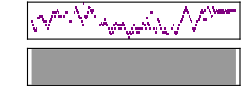

```mathematica
fromCodedNoteString[generateSample[trainedNet3,"+c+a+S+R+S e+++f+++++",500],100]
```

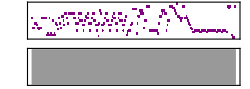

```mathematica
fromCodedNoteString[generateSample[trainedNet3,"   ",500],100]
```

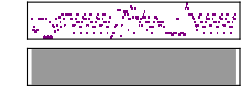

```mathematica
fromCodedNoteString[generateSample[trainedNet3,"   ",500],120]
```

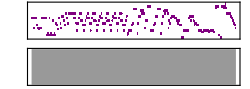

```mathematica
fromCodedNoteString[generateSample[trainedNet3,"   ",500],120]
```

#### Import a pre learned net with 100 memory cells

With one 100 LSTM layer. Trained for 7 hours. Not finished training. Seems to have learned the sequences quite a lot.

```mathematica
trainedNet3=Import[FileNameJoin[{NotebookDirectory[],"FluteNets","2017-09-21T23:57:25_20_2423_48441_3.78e-2.wlnet"}]]
```

NetChain[]

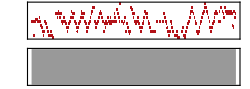
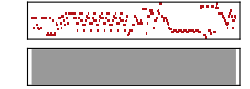
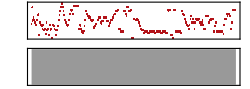
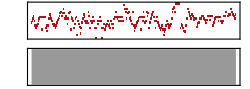
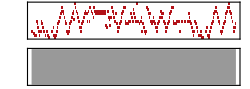

```mathematica
{#,toWAVSound[#]}&/@(fromCodedNoteString[generateSample[trainedNet3,#,500],90]&/@{"    ","    ","ancdef","abcdef","S++ R++ Q++"})
```

#### Try with 50 memory cells

```mathematica
trainedNet3=Import[FileNameJoin[{NotebookDirectory[],"FluteNets","2017-09-22T12:05:48_31_0973_19441_2.53e-1.wlnet"}]]
```

NetChain[]

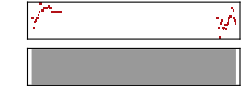
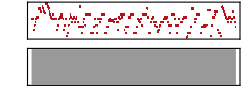
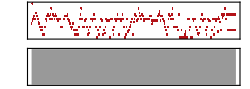
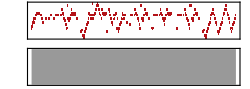
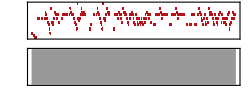

```mathematica
{#,toWAVSound[#]}&/@(fromCodedNoteString[generateSample[trainedNet3,#,500],90]&/@{"    ","    ","ancdef","abcdef","S++ R++ Q++"})
```

#### What will happen with just 30 memory cells?

Trained for 8 hours.

This is sounding more like new material !

```mathematica
trainedNet3=Import[FileNameJoin[{NotebookDirectory[],"FluteNets","2017-09-22T23:16:35_33_7189_143770_3.16e-1.wlnet"}]]
```

NetChain[]

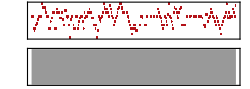
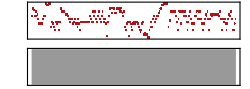
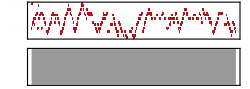
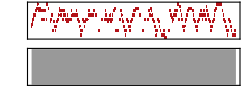
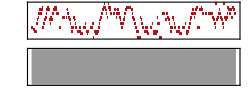

```mathematica
{#,toWAVSound[#]}&/@(fromCodedNoteString[generateSample[trainedNet3,#,500],90]&/@{"    ","    ","ancdef","abcdef","S++ R++ Q++"})
```

#### How about just 10 memory cells?

Trained for 4 hours

```mathematica
trainedNet3=Import[FileNameJoin[{NotebookDirectory[],"FluteNets","2017-09-23T09:54:06_35_04421_088401_7.86e-1.wlnet"}]]
```

NetChain[]

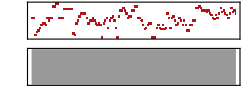
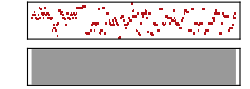
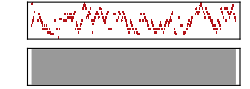
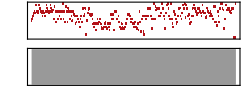
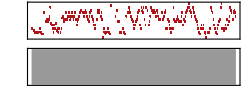

```mathematica
{#,toWAVSound[#]}&/@(fromCodedNoteString[generateSample[trainedNet3,#,500],90]&/@{"    ","    ","ancdef","abcdef","S++ R++ Q++"})
```

#### How about just 5 memory cells?

Trained for 4 hours

```mathematica
trainedNet3=Import[FileNameJoin[{NotebookDirectory[],"FluteNets","2017-09-23T12:42:34_37_07227_144521_1.13e+0.wlnet"}]]
```

NetChain[]

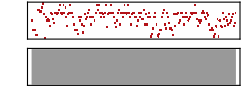
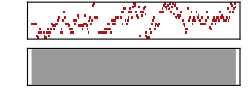
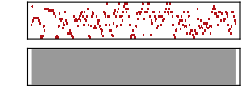
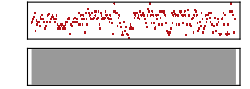
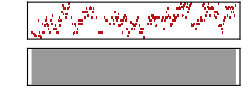

```mathematica
{#,toWAVSound[#]}&/@(fromCodedNoteString[generateSample[trainedNet3,#,500],90]&/@{"    ","    ","ancdef","abcdef","S++ R++ Q++"})
```

#### How about just 1 memory cell?

```mathematica
trainedNet3=Import[FileNameJoin[{NotebookDirectory[],"FluteNets","2017-09-23T16:49:22_39_03748_074941_1.54e+0.wlnet"}]]
```

NetChain[]

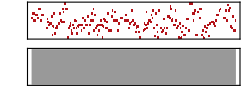
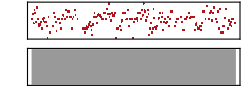
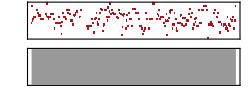
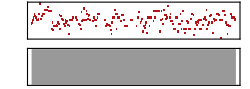
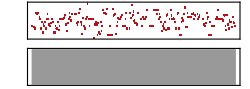

```mathematica
{#,toWAVSound[#]}&/@(fromCodedNoteString[generateSample[trainedNet3,#,500],90]&/@{"    ","    ","ancdef","abcdef","S++ R++ Q++"})
```

#### Export as MIDI file

```mathematica
Export["/tmp/a.mid",%]
```

/tmp/a.mid

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["/tmp/a.mid"]]]
```

#### Export as MXNet file!

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"MXNet","BachFragments3.json"}],trainedNet3,"MXNet"]
```

/Users/peter.sjogren/Google Drive/Mathematica/bach/MXNet/BachFragments3.json